```mathematica
d=146.0  (*grating periodic distance of silica*)
Subscript[ρ, sil]=23.0*10^-4 (*scattering length density of silica*)
Subscript[ρ, coat]=1.0*Subscript[ρ, sil]
g=2*π/d (*resiprocal lattice length*)
f=51/100(*filling factor of grating*)
fb=47/100
ft=43/100
t=30.0  (*tickness of grating *)
tc=15.0(*tickness of coated layer*)
Subscript[f, new]=0.0 (*filling factor of coated layer*)
```

146.

0.0023

0.0023

0.0430355

51/100

47/100

43/100

30.

15.

0.

-0.0000673772

0.00211143

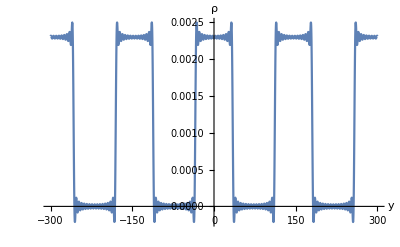

```mathematica
j=30;
<<FourierSeries`
Quiet[Table[Subscript[ρc, m]=Re[NFourierCoefficient[Subscript[ρ, sil]*UnitStep[Cos[g*y/(2*fb)]],y,m, FourierParameters->{1, g} ]],{m,-2j,2j}]];
Subscript[ρc, 4]
ρ1[y_,j_] := Sum[Subscript[ρc, m]*Cos[g*y*m],{m,-j,j}]
ρ1[Pi,4]
Plot[ρ1[y,30],{y,-300,300},  AxesLabel->{Style["y",Bold,16],Style["ρ",Bold,16],FontSize[40]},PlotRange->All,AxesOrigin->{0,0}]
```

-0.000242955

0.00217169

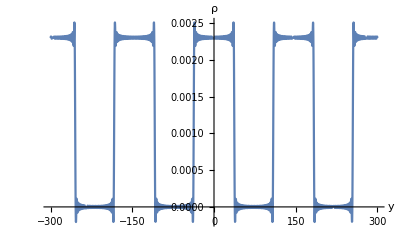

```mathematica
j=30;
<<FourierSeries`
(*Quiet[Table[Subscript[ρs, m]=Re[NFourierCoefficient[Subscript[ρ, coat]*UnitStep[Cos[g*y/(2*f)]],y,m, FourierParameters->{1, g} ]],{m,-2j,2j}]];*)
Quiet[Table[Subscript[ρs, m]=Re[NFourierCoefficient[Subscript[ρ, sil]*UnitStep[Cos[g*y/(2*f)]],y,m, FourierParameters->{1, g} ]],{m,-2j,2j}]];
Subscript[ρs, 3]
ρ3[y_,j_] := Sum[Subscript[ρs, m]*Cos[g*y*m],{m,-j,j}]
ρ3[Pi,4]
Plot[ρ3[y,50],{y,-300,300},  AxesLabel->{Style["y",Bold,16],Style["ρ",Bold,16],FontSize[40]},PlotRange->All,AxesOrigin->{0,0}]
(*Manipulate[Plot[ρ2[y,j],{y,-140,140},  AxesLabel->{Style["y",Bold,16],Style["ρ",Bold,16],FontSize[40]}],{j,0,50}]*)
```

```mathematica
-(t+Subscript[t, c])<z<-t: ρ(|y|<fd/2 )=Subscript[ρ, sil] & ρ(|y|>fd/2)=Subscript[ρ, c] :
```

-0.000141026

0.00210915

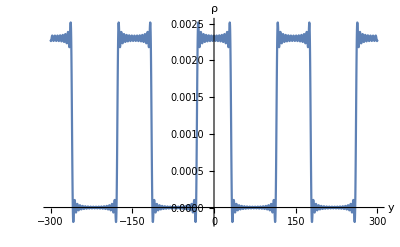

```mathematica
j=30;
<<FourierSeries`
Quiet[Table[Subscript[ρb, m]=Re[NFourierCoefficient[Subscript[ρ, sil]*UnitStep[Cos[g*y/(2*ft)]],y,m, FourierParameters->{1, g} ]],{m,-2j,2j}]];
Subscript[ρb, 4]
ρ5[y_,j_] := Sum[Subscript[ρb, m]*Cos[g*y*m],{m,-j,j}]
ρ5[Pi,4]
Plot[ρ5[y,30],{y,-300,300},  AxesLabel->{Style["y",Bold,16],Style["ρ",Bold,16],FontSize[40]},PlotRange->All,AxesOrigin->{0,0}]
(*ρ3[y_,j_] := Sum[Subscript[ρ, b]*Cos[g*y*m],{m,-j,j}]*)
(*Manipulate[Plot[ρ3[y,j],{y,-140,140},  AxesLabel->{Style["y",Bold,16],Style["ρ",Bold,16],FontSize[40]}],{j,0,50}]*)
```

```mathematica
Plot3D[(UnitStep[-z]-UnitStep[-z-tc])*ρ1[y,30]+(UnitStep[-z-tc]-UnitStep[-z-t])*ρ3[y,30]+(UnitStep[-z-t]-UnitStep[-z-tc-t])*ρ5[y,30]+(UnitStep[-z-t-tc])*Subscript[ρ, sil],{z,-300,300},{y,-200,200},AxesLabel->{Style["Z",Bold,16],Style["y",Bold,16],Style["ρ",Bold,16]}]
```

-Graphics3D-

```mathematica
j=25;
Subscript[θ, 0]=0.20*π/180;
For[h=1;λ=0.077012,λ ≤0.077012,λ =λ +0.001,
For[s=1;ϕ=-10.0*π/180,ϕ≤10.0*π/180,ϕ=ϕ+0.05*π/180;
Subscript[k, y,s,h]=Subscript[k, iy]=(2π)/λ*Sin[ϕ];
Subscript[k, z,s,h]=Subscript[k, iz]=(2π)/λ*Sin[Subscript[θ, 0]];
Subscript[newkz, s,h]=((2 π)/λ)*Sin[Subscript[θ, 0]];
Subscript[phi, s]=ϕ;
Subscript[newky, s,h]=(2π)/λ*Sin[ϕ];
(*Schrodinger equation in the region I*)
F1[n_,m_]:=(-(Subscript[k, iy]+n*g)^2+Subscript[k, iz]^2+Subscript[k, iy]^2)*KroneckerDelta[n,m];
V1[n_,m_]:=-4*π*Subscript[ρc, n-m];
M1=Table[F1[n,m]+V1[n,m],{n,-j,j},{m,-j,j}];
{vals1,vecs1}=Eigensystem[M1];


(*Schrodinger equation in region*)
F2[n_,m_]:=(-(Subscript[k, iy]+n*g)^2+Subscript[k, iz]^2+Subscript[k, iy]^2)*KroneckerDelta[n,m];
V2[n_,m_]:=-4*π*Subscript[ρs, n-m];
M2=Table[F2[n,m]+V2[n,m],{n,-j,j},{m,-j,j}];
{vals2,vecs2}=Eigensystem[M2];


(*Schrodinger equation in region III*)
F3[n_,m_]:=(-(Subscript[k, iy]+n*g)^2+Subscript[k, iz]^2+Subscript[k, iy]^2)*KroneckerDelta[n,m];
V3[n_,m_]:=-4*π*Subscript[ρb, n-m];
M3=Table[F3[n,m]+V3[n,m],{n,-j,j},{m,-j,j}];
{vals3,vecs3}=Eigensystem[M3];


(*Wave vector in different region based on conservation energy*)
Table[(*Subscript[p0, s]=*) Subscript[X, s,h,n]=Subscript[x, n]=Sqrt[Subscript[k, iy]^2+Subscript[k, iz]^2-(Subscript[k, iy]+n*g)^2],{n,-j,j}];
Table[(*Subscript[p1, s]=*)Subscript[kz1, s,h,n]=Subscript[k1, z,n]=Sqrt[vals1[[n+j+1]]],{n,-j,j}];
Table[(*Subscript[p2, s]=*)Subscript[kz2, s,h,n]=Subscript[k2, z,n]=Sqrt[vals2[[n+j+1]]],{n,-j,j}];
Table[(*Subscript[p3, s]=*)Subscript[kz3, s,h,n]=Subscript[k3, z,n]=Sqrt[vals3[[n+j+1]]],{n,-j,j}];
Table[Subscript[Pt, s,h,n]=Subscript[p, n]=Sqrt[Subscript[k, iy]^2+Subscript[k, iz]^2-4*π*Subscript[ρ, sil]-(Subscript[k, iy]+n*g)^2],{n,-j,j}];
(*And the eigenvector coefficients are:*)
Table[Subscript[b1, n,m]=vecs1[[n+j+1,m+j+1]],{n,-j,j},{m,-j,j}];
Table[Subscript[b2, n,m]=vecs2[[n+j+1,m+j+1]],{n,-j,j},{m,-j,j}];
Table[Subscript[b3, n,m]=vecs3[[n+j+1,m+j+1]],{n,-j,j},{m,-j,j}];

(*Applying series of boundary condition*)
Arr={Table[KroneckerDelta[m,0]+Subscript[r, 0,m]-Sum[(Subscript[t, 1,n]+Subscript[r, 1,n]*ⅇ^(ⅈ*Subscript[k1, z,n]*tc))*Subscript[b1, n,m],{n,-j,j}]==0,{m,-j,j}],Table[-Subscript[k, iz]*KroneckerDelta[m,0]+Subscript[x, m]*Subscript[r, 0,m]+Sum[Subscript[k1, z,n]*(Subscript[t, 1,n]-Subscript[r, 1,n]*ⅇ^(ⅈ*Subscript[k1, z,n]*tc))*Subscript[b1, n,m],{n,-j,j}]==0,{m,-j,j}],

Table[Sum[(Subscript[r, 1,n]+Subscript[t, 1,n]*ⅇ^(ⅈ*Subscript[k1, z,n]*tc))*Subscript[b1, n,m],{n,-j,j}]-Sum[(Subscript[t, 2,n]+Subscript[r, 2,n]*ⅇ^(ⅈ*Subscript[k2, z,n]*(t-tc)))*Subscript[b2, n,m],{n,-j,j}]==0,{m,-j,j}],Table[Sum[Subscript[k1, z,n]*(Subscript[r, 1,n]-Subscript[t, 1,n]*ⅇ^(ⅈ*Subscript[k1, z,n]*tc))*Subscript[b1, n,m],{n,-j,j}]-Sum[Subscript[k2, z,n]*(-Subscript[t, 2,n]+Subscript[r, 2,n]*ⅇ^(ⅈ*Subscript[k2, z,n]*(t-tc)))*Subscript[b2, n,m],{n,-j,j}]==0,{m,-j,j}],

Table[Sum[(Subscript[r, 2,n]+Subscript[t, 2,n]*ⅇ^(ⅈ*Subscript[k2, z,n]*(t-tc)))*Subscript[b2, n,m],{n,-j,j}]-Sum[(Subscript[t, 3,n]+Subscript[r, 3,n]*ⅇ^(ⅈ*Subscript[k3, z,n]*tc))*Subscript[b3, n,m],{n,-j,j}]==0,{m,-j,j}],Table[Sum[Subscript[k2, z,n]*(Subscript[r, 2,n]-Subscript[t, 2,n]*ⅇ^(ⅈ*Subscript[k2, z,n]*(t-tc)))*Subscript[b2, n,m],{n,-j,j}]-Sum[Subscript[k3, z,n]*(-Subscript[t, 3,n]+Subscript[r, 3,n]*ⅇ^(ⅈ*Subscript[k3, z,n]*tc))*Subscript[b3, n,m],{n,-j,j}]==0,{m,-j,j}],


Table[Sum[(Subscript[t, 3,n]*ⅇ^(ⅈ*Subscript[k3, z,n]*tc)+Subscript[r, 3,n])*Subscript[b3, n,m],{n,-j,j}]-Subscript[t, 4,m]==0,{m,-j,j}],Table[Sum[Subscript[k3, z,n]*(-Subscript[t, 3,n]*ⅇ^(ⅈ*Subscript[k3, z,n]*tc)+Subscript[r, 3,n])*Subscript[b3, n,m],{n,-j,j}]+Subscript[p, m]*Subscript[t, 4,m]==0,{m,-j,j}]};

arr=Flatten[Arr];

lis={Table[Subscript[r, 0,n],{n,-j,j}],Table[Subscript[r, 1,n],{n,-j,j}],Table[Subscript[t, 1,n],{n,-j,j}],Table[Subscript[r, 2,n],{n,-j,j}],Table[Subscript[t, 2,n],{n,-j,j}],Table[Subscript[r, 3,n],{n,-j,j}],Table[Subscript[t, 3,n],{n,-j,j}],Table[Subscript[t, 4,n],{n,-j,j}] };
list=Flatten[lis];

Sol=Solve[arr,list];
Table[Subscript[RF, s,h,n]=Subscript[R, 0,n]=Sol[[1]][[n+j+1,2]],{n,-j,j}];
Table[Subscript[R, 1,n]=Sol[[1]][[n+j+1+(2j+1),2]],{n,-j,j}];
Table[Subscript[T, 1,n]=Sol[[1]][[n+j+1+2*(2j+1),2]],{n,-j,j}];
Table[Subscript[R, 2,n]=Sol[[1]][[n+j+1+3*(2j+1),2]],{n,-j,j}];
Table[Subscript[T, 2,n]=Sol[[1]][[n+j+1+4*(2j+1),2]],{n,-j,j}];
Table[Subscript[R, 3,n]=Sol[[1]][[n+j+1+5*(2j+1),2]],{n,-j,j}];
Table[Subscript[T, 3,n]=Sol[[1]][[n+j+1+6*(2j+1),2]],{n,-j,j}];
Table[Subscript[TF, s,h,n]=Subscript[T, 2,n]=Sol[[1]][[n+j+1+7*(2j+1),2]],{n,-j,j}];
(*Condition to avoid unphysical and decaying solutions:*)
Table[If[Im[Subscript[X, s,h,n]]≠0,Subscript[Rf, s,h,n]=0,Subscript[Rf, s,h,n]=Subscript[RF, s,h,n]],{n,-j,j}];
Table[If[Im[Subscript[Pt, s,h,n]]≠0,Subscript[Tf, s,h,n]=0,Subscript[Tf, s,h,n]=Subscript[TF, s,h,n]],{n,-j,j}];
(*Print[Subscript[k, y,s,1],Subscript[k, z,s,1]];*)
(*Print[s];*)
s=s+1];
Print[h];
h=h+1]
```

1

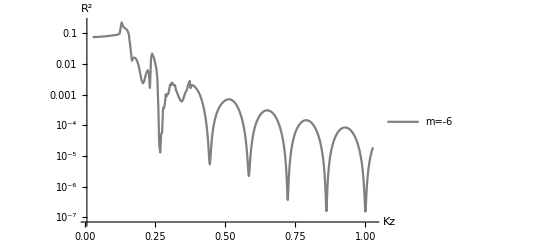

```mathematica
Show[
ListLinePlot[Table[{Re[Subscript[X, s,1,-1]],(1*Abs[Subscript[Rf, s,1,-1]])^2},{s,1,1200}],ScalingFunctions->"Log", PlotStyle-> {Gray,Solid},PlotRange-> All,PlotLegends->{"m=-6"}],
AxesLabel->{Style[Kz,FontSize->14,FontColor->Black],Style["R"^2,FontSize->14,FontColor->Black]},AxesStyle->10]
```

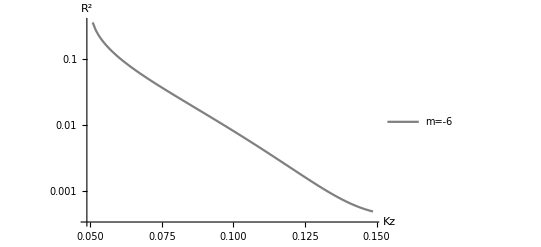

```mathematica
Show[
ListLinePlot[Table[{Re[Subscript[X, s,1,-1]],(1*Abs[Subscript[Tf, s,1,-1]])^2},{s,1,400}],ScalingFunctions->"Log", PlotStyle-> {Gray,Solid},PlotRange-> All,PlotLegends->{"m=-6"}],
AxesLabel->{Style[Kz,FontSize->14,FontColor->Black],Style["R"^2,FontSize->14,FontColor->Black]},AxesStyle->10]
```

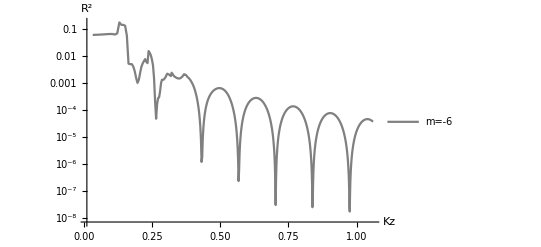

```mathematica
Show[
ListLinePlot[Table[{Re[Subscript[X, s,1,-1]],(1*Abs[Subscript[Rf, s,1,-1]])^2},{s,1,1200}],ScalingFunctions->"Log", PlotStyle-> {Gray,Solid},PlotRange-> All,PlotLegends->{"m=-6"}],
AxesLabel->{Style[Kz,FontSize->14,FontColor->Black],Style["R"^2,FontSize->14,FontColor->Black]},AxesStyle->10]
```

```mathematica
For[i=-15, i<1, i++,bigmatrxw=Table[{Re[Subscript[X, s,1,i]],(1*Abs[Subscript[Rf, s,1,i]])^2},{s,1,1200}];
Export["C:\\Users\\hrahmani\\Desktop\\x-ray project\\presentation\\sample_for_invest\\reflectivity\\rod="<>ToString[i]<>".txt",bigmatrxw,"Table"];Print[i]]
```

-15

-14

-13

-12

-11

-10

-9

-8

-7

-6

-5

-4

-3

-2

-1

0

```mathematica
For[i=-15, i<1, i++,bigmatrxw=Table[{Re[Subscript[X, s,1,i]],(1*Abs[Subscript[Tf, s,1,i]])^2},{s,1,1200}];
Export["C:\\Users\\hrahmani\\Desktop\\x-ray project\\presentation\\sample_for_invest\\transmissivity\\rod="<>ToString[i]<>".txt",bigmatrxw,"Table"];Print[i]]
```

-15

-14

-13

-12

-11

-10

-9

-8

-7

-6

-5

-4

-3

-2

-1

0

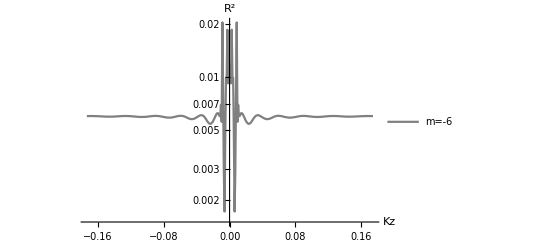

```mathematica
Show[
ListLinePlot[Table[{Subscript[phi, s],(((Subscript[X, s,1,0])/Subscript[k, iz])*Abs[Subscript[Rf, s,1,0]])^2},{s,1,400}],ScalingFunctions->"Log", PlotStyle-> {Gray,Solid},PlotRange-> All,PlotLegends->{"m=-6"}],
AxesLabel->{Style[Kz,FontSize->14,FontColor->Black],Style["R"^2,FontSize->14,FontColor->Black]},AxesStyle->10]
```

```mathematica
Show[
ListLinePlot[Table[{Subscript[phi, s],((Subscript[Pt, s,1,0])/Subscript[k, iz])*(Abs[Subscript[Tf, s,1,0]])^2},{s,1,400}],ScalingFunctions->"Log", PlotStyle-> {Gray,Solid},PlotRange-> All,PlotLegends->{"m=-6"}],
AxesLabel->{Style[Kz,FontSize->14,FontColor->Black],Style["R"^2,FontSize->14,FontColor->Black]},AxesStyle->10]
```

-Graphics-

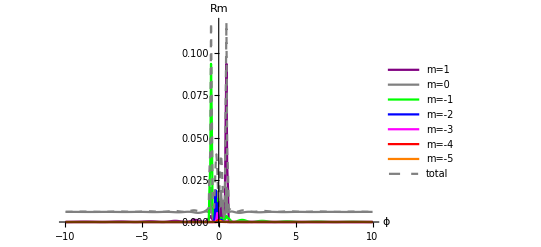

```mathematica
Show[ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,1]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,1]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Purple,Thick},PlotRange->All,PlotLegends->{"m=1"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,0]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,0]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Gray,Thick},PlotRange->All,PlotLegends->{"m=0"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,-1]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,-1]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Green,Thick},PlotRange->All,PlotLegends->{"m=-1"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,-2]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,-2]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Blue,Thick},PlotRange->All,PlotLegends->{"m=-2"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,-3]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,-3]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Magenta,Thick},PlotRange->All,PlotLegends->{"m=-3"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,-4]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,-4]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Red,Thick},PlotRange->All,PlotLegends->{"m=-4"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[X,s,1,-5]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,-5]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Orange,Thick},PlotRange->All,PlotLegends->{"m=-5"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,Sum[(Subscript[X,s,1,l]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,l]])^2,{l,-5,5}]},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Gray,Dashed},PlotRange->All,PlotLegends->{"total"}],PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"ϕ","Rm"}]
```

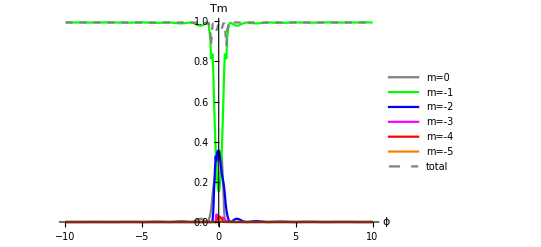

```mathematica
Show[ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,1]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,1]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Gray,Thick},PlotRange->All,PlotLegends->{"m=0"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,0]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,0]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Green,Thick},PlotRange->All,PlotLegends->{"m=-1"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,-1]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,-1]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Blue,Thick},PlotRange->All,PlotLegends->{"m=-2"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,-2]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,-2]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Magenta,Thick},PlotRange->All,PlotLegends->{"m=-3"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,-3]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,-3]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Red,Thick},PlotRange->All,PlotLegends->{"m=-4"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,(Subscript[Pt,s,1,-4]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,-4]])^2},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Orange,Thick},PlotRange->All,PlotLegends->{"m=-5"}],ListLinePlot[Table[{Subscript[phi,s]*180/Pi,Sum[(Subscript[Pt,s,1,l]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,l]])^2,{l,-10,10}]},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Gray,Dashed},PlotRange->All,PlotLegends->{"total"}],PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"ϕ","Tm"}]
```

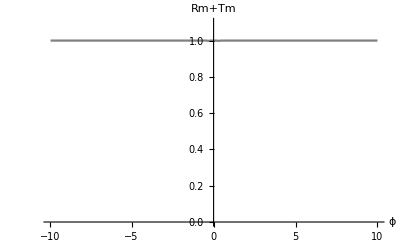

```mathematica
Show[ListLinePlot[Table[{Subscript[phi,s]*180/Pi,Sum[(Subscript[X,s,1,l]/Subscript[k,iz])*(Abs[Subscript[Rf,s,1,l]])^2+(Subscript[Pt,s,1,l]/Subscript[k,iz])*(Abs[Subscript[Tf,s,1,l]])^2,{l,-15,15}]},{s,0,400}],AxesOrigin->{0,0},PlotStyle->{Gray,Solid},PlotRange->All],PlotRange->{0,1.1},AxesOrigin->{0,0},AxesLabel->{"ϕ","Rm+Tm"}]
```